### H[] is the core matrix for hamiltonian in k-space, there are 3 different sites， every site has two components.

```mathematica
H[kx_,ky_]:=-I({{0, 2, 0, 1+Exp[I(kx/2-ky Sqrt[3]/2)], 0, 1+Exp[I kx]}, {-2, 0, (1+Exp[I (kx/2-ky Sqrt[3]/2)])/2, 0, (1+Exp[I kx])/2, 0}, {0, 1+Exp[I(-kx/2+ky Sqrt[3]/2)], 0, 2, 0, 1+Exp[I(kx/2+ky Sqrt[3]/2)]}, {(1+Exp[I(-kx/2+ky Sqrt[3]/2)])/2, 0, -2, 0, (1+Exp[I(kx/2+ky Sqrt[3]/2)])/2, 0}, {0, 1+Exp[-I kx], 0, 1+Exp[-I(kx/2+ky Sqrt[3]/2)], 0, 2}, {(1+Exp[-I kx])/2, 0, (1+Exp[-I(kx/2+ky Sqrt[3]/2)])/2, 0, -2, 0}});
```

```mathematica
MatrixForm[H[X,Y]]
```

(0 | -2 ⅈ | 0 | -ⅈ (1+ⅇ^(ⅈ (X/2-(√3 Y)/2))) | 0 | -ⅈ (1+ⅇ^(ⅈ X))
2 ⅈ | 0 | -1/2 ⅈ (1+ⅇ^(ⅈ (X/2-(√3 Y)/2))) | 0 | -1/2 ⅈ (1+ⅇ^(ⅈ X)) | 0
0 | -ⅈ (1+ⅇ^(ⅈ (-X/2+(√3 Y)/2))) | 0 | -2 ⅈ | 0 | -ⅈ (1+ⅇ^(ⅈ (X/2+(√3 Y)/2)))
-1/2 ⅈ (1+ⅇ^(ⅈ (-X/2+(√3 Y)/2))) | 0 | 2 ⅈ | 0 | -1/2 ⅈ (1+ⅇ^(ⅈ (X/2+(√3 Y)/2))) | 0
0 | -ⅈ (1+ⅇ^(-ⅈ X)) | 0 | -ⅈ (1+ⅇ^(-ⅈ (X/2+(√3 Y)/2))) | 0 | -2 ⅈ
-1/2 ⅈ (1+ⅇ^(-ⅈ X)) | 0 | -1/2 ⅈ (1+ⅇ^(-ⅈ (X/2+(√3 Y)/2))) | 0 | 2 ⅈ | 0)

### Dispersion relation E[kx,ky]

```mathematica
Eigensystem[H[kx,ky]]
```

{{0,0,-(ⅇ^(-(ⅈ kx)/2-1/4 ⅈ √3 ky) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)))/(√2),-(ⅇ^(-(ⅈ kx)/2-1/4 ⅈ √3 ky) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)))/(√2),(ⅇ^(-(ⅈ kx)/2-1/4 ⅈ √3 ky) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)))/(√2),(ⅇ^(-(ⅈ kx)/2-1/4 ⅈ √3 ky) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)))/(√2)},{{0,(ⅇ^((ⅈ kx)/2) (-1+ⅇ^((ⅈ kx)/2+1/2 ⅈ √3 ky)))/(ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)),0,(ⅇ^(1/2 ⅈ √3 ky) (-1+ⅇ^(ⅈ kx)))/(-ⅇ^((ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)),0,1},{0,0,0,0,0,0},{-(√2 ⅇ^((ⅈ kx)/2+1/4 ⅈ √3 ky) (-1+ⅇ^(ⅈ kx)) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)))/(-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)),-(ⅇ^(ⅈ kx) (ⅇ^((ⅈ kx)/2)-3 ⅇ^(1/2 ⅈ √3 ky)+3 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)-ⅇ^((ⅈ kx)/2+ⅈ √3 ky)))/(-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)),-(√2 ⅇ^((ⅈ kx)/2+1/4 ⅈ √3 ky) (-1+ⅇ^((ⅈ kx)/2+1/2 ⅈ √3 ky)) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)))/(-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)),-(4 ⅇ^(3 ⅈ kx+3/2 ⅈ √3 ky) (1+ⅇ^(-ⅈ kx)) (ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2)))+(-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2)))) (-8 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2)))+4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx)) (1+ⅇ^(ⅈ (kx/2+(√3 ky)/2)))))/(-4 ⅇ^(3 ⅈ kx+3/2 ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))^2 (ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky))+(8 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2)))) (-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2))))),0,1},{(ⅇ^(ⅈ kx) (-ⅇ^((ⅈ kx)/2)-3 ⅇ^(1/2 ⅈ √3 ky)+3 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)))/(-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)),-(ⅇ^((ⅈ kx)/2+1/4 ⅈ √3 ky) (-1+ⅇ^(ⅈ kx)) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)))/(√2 (-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky))),(ⅇ^((ⅈ kx)/2+1/2 ⅈ √3 ky) (-3 ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+3 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)))/(-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)),-(-2 √2 ⅇ^((3 ⅈ kx)/2+3/4 ⅈ √3 ky) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2))))-2 √2 ⅇ^((3 ⅈ kx)/2+3/4 ⅈ √3 ky) (1+ⅇ^(-ⅈ kx)) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)) (4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2)))+ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx)) (1+ⅇ^(ⅈ (kx/2+(√3 ky)/2)))))/(-4 ⅇ^(3 ⅈ kx+3/2 ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))^2 (ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky))+(8 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2)))) (-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2))))),1,0},{(√2 ⅇ^((ⅈ kx)/2+1/4 ⅈ √3 ky) (-1+ⅇ^(ⅈ kx)) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)))/(-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)),-(ⅇ^(ⅈ kx) (ⅇ^((ⅈ kx)/2)-3 ⅇ^(1/2 ⅈ √3 ky)+3 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)-ⅇ^((ⅈ kx)/2+ⅈ √3 ky)))/(-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)),(√2 ⅇ^((ⅈ kx)/2+1/4 ⅈ √3 ky) (-1+ⅇ^((ⅈ kx)/2+1/2 ⅈ √3 ky)) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)))/(-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)),-(4 ⅇ^(3 ⅈ kx+3/2 ⅈ √3 ky) (1+ⅇ^(-ⅈ kx)) (ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2)))+(-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2)))) (-8 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2)))+4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx)) (1+ⅇ^(ⅈ (kx/2+(√3 ky)/2)))))/(-4 ⅇ^(3 ⅈ kx+3/2 ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))^2 (ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky))+(8 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2)))) (-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2))))),0,1},{(ⅇ^(ⅈ kx) (-ⅇ^((ⅈ kx)/2)-3 ⅇ^(1/2 ⅈ √3 ky)+3 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)))/(-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)),(ⅇ^((ⅈ kx)/2+1/4 ⅈ √3 ky) (-1+ⅇ^(ⅈ kx)) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)))/(√2 (-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky))),(ⅇ^((ⅈ kx)/2+1/2 ⅈ √3 ky) (-3 ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+3 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)))/(-ⅇ^((ⅈ kx)/2)-ⅇ^(1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)),-(2 √2 ⅇ^((3 ⅈ kx)/2+3/4 ⅈ √3 ky) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2))))+2 √2 ⅇ^((3 ⅈ kx)/2+3/4 ⅈ √3 ky) (1+ⅇ^(-ⅈ kx)) √(ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)) (4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2)))+ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx)) (1+ⅇ^(ⅈ (kx/2+(√3 ky)/2)))))/(-4 ⅇ^(3 ⅈ kx+3/2 ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))^2 (ⅇ^((ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2)+ⅇ^(1/2 ⅈ √3 ky)-6 ⅇ^(ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^(2 ⅈ kx+1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+ⅈ √3 ky)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky))+(8 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2)))) (-4 ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(-ⅈ kx))-ⅇ^(2 ⅈ kx+ⅈ √3 ky) (1+ⅇ^(ⅈ (-kx/2+(√3 ky)/2))) (1+ⅇ^(-ⅈ (kx/2+(√3 ky)/2))))),1,0}}}

```mathematica
EE[kx_,ky_]:=Sort[Re[Eigenvalues[H[kx,ky]]]];
```

```mathematica
N[EE[Pi/2,Pi/2]]
```

{0.,0.,-1.64456,-1.64456,1.64456,1.64456}

### 3D Plot

```mathematica
Plot3D[EE[x,y],{x,-2Pi/Sqrt[3],2Pi/Sqrt[3]},{y,- Pi, Pi},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤2Pi/Sqrt[3]&&Abs[x-y/Sqrt[3]]≤2Pi/Sqrt[3]],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

### 1D High symmetry Brillouin zone point loop plot

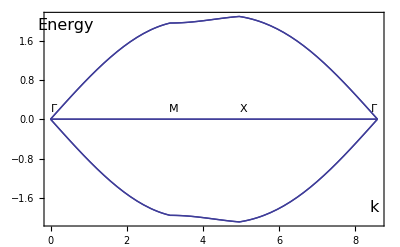

```mathematica
Plot[Piecewise[{{EE[t Sqrt[3]/2,t/2],t≥0&&t<Pi},{EE[((t-Pi)+Pi Sqrt[3])/2,(Pi+Pi/Sqrt[3]-t)Sqrt[3]/2],t≥Pi&&t<Pi+Pi/Sqrt[3]},{EE[Pi+Sqrt[3] Pi-t,0],t≥Pi+Pi/Sqrt[3]&&t<Pi+Pi Sqrt[3]}}],{t,0,Pi+Sqrt[3] Pi},GridLines->{{{Pi,Dashed},{Pi+Pi/Sqrt[3],Dashed},{0,Dashed},{Pi+Pi Sqrt[3],Dashed}},{}},Epilog->{Inset["Γ",{0.1,0.2}],Inset["M",{Pi+0.1,0.2}],Inset["X",{Pi+Pi/Sqrt[3]+0.1,0.2}],Inset["Γ",{Pi+Pi Sqrt[3]-0.1,0.2}],Inset[Style["k",16],{8.5,-1.8}],Inset[Style["Energy",16],{0.4,1.9}]},Frame->True]
```

```mathematica
EEE[x_,y_]:={-1-√(3+2 Cos[x Sqrt[3]]+2 Cos[√3 x/2- 3y/2]+2 Cos[Sqrt[3]x/2+3 y/2]),-1+√(3+2 Cos[Sqrt[3]x]+2 Cos[Sqrt[3]x/2-3 y/2]+2 Cos[Sqrt[3]x/2+3 y/2])}
```

```mathematica
Array[EN,400];
```

```mathematica
nn=1;While[nn<401,EN[nn]=0;nn++];
```

```mathematica
For[i=0,i≤200,i++,
For[j=0,j≤200,j++,
{
energy=EEE[i Pi/Sqrt[3]/100-Pi/Sqrt[3],2j Pi/3/100-2Pi/3]//N;    (* make sure energy is represented in the form 1.234 and not Cos[...] *)
n=Rescale[energy[[1]],{-4.5,2.2},{1,400}]//Round;    (* find appropriate bin for band 1*)
EN[n]++;
n=Rescale[energy[[2]],{-4.5,2.2},{1,400}]//Round;    (* find appropriate bin for band 2*)
EN[n]++
}
]
]
```

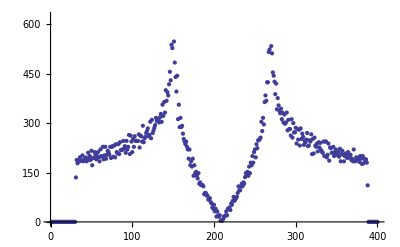

```mathematica
ListPlot[Table[{i,EN[i]},{i,1,400}]]
```

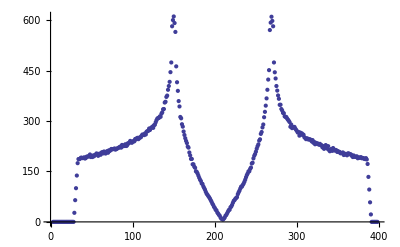

```mathematica
ListPlot[Table[{i,(EN[i-1]+EN[i-2]+EN[i]+EN[i+1]+EN[i+2])/5},{i,3,398}]]
```